```mathematica
s=0.5;
b=3;
c=1;
fc[x_]:=1-s;
```

```mathematica
fd[x_]:=1;
```

```mathematica
fa[x_]:=1+s*b*x-s*c;
fb[x_]:=1+s*b*x;
fo[x_]:=x*fa[x]+(1-x)*fb[x];
```

```mathematica
f[x_]:=x*fc[x]+(1-x)fd[x]
```

```mathematica
Evaluate[fc[x]/f[x]]
```

0.5/(1-0.5 x)

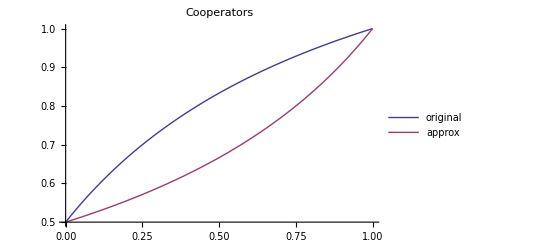

```mathematica
Plot[{Evaluate[fa[x]/fo[x]],Evaluate[fc[x]/f[x]]},{x,0,1},PlotLegends->Placed[{"original","approx"},{0.8,0.4}],PlotLabel->"Cooperators"]
```

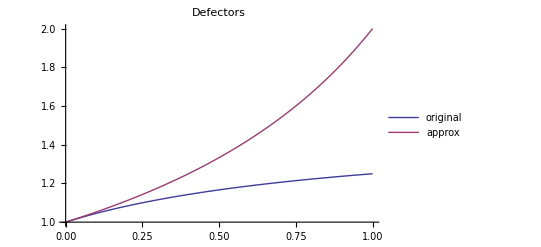

```mathematica
Plot[{Evaluate[fb[x]/fo[x]],Evaluate[fd[x]/f[x]]},{x,0,1},PlotLegends->Placed[{"original","approx"},{0.8,0.6}],PlotLabel->"Defectors"]
```